# NG^23 T_02. Наивный байесовский классификатор

КМ2021, курс 2, семестр 4
Ковалевская В.С.
16-фев-2023

## Задание 1

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
{dig = 9,row = 17,col = 20,ind=28 (row-1)+col}
```

{9,17,20,468}

```mathematica
ClearAll[indFriend]
indFriend=Flatten@Position[Train[[1]],dig];
Length[indFriend]
```

5949

```mathematica
ClearAll[indFoe]
Length[indFoe=Flatten@Position[Train[[1]],Except@dig,Heads->False]]
```

54051

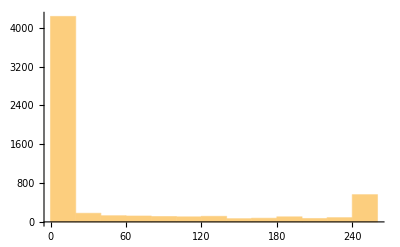

```mathematica
Histogram[Train[[2,indFriend,ind]]]
```

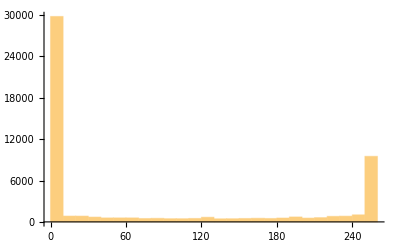

```mathematica
Histogram[Train[[2,indFoe,ind]]]
```

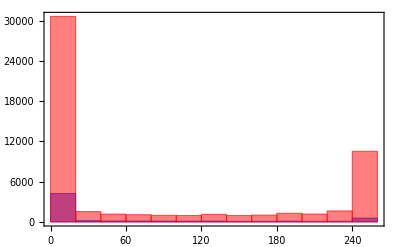

```mathematica
Histogram[{Train[[2,indFriend,ind]],Train[[2,indFoe,ind]]},15,ChartStyle->{Blue,Red},Frame->True]
```

## Задание 2

SparseArray[…]

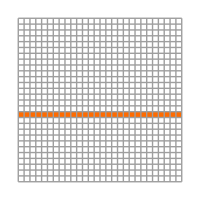

```mathematica
SparseArray[{row,_}->1.,{28,28}]
MatrixPlot[%,ImageSize->200,Mesh->All,Frame->False]
```

SparseArray[…]

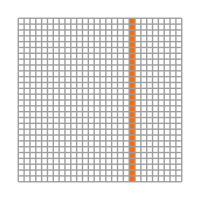

```mathematica
SparseArray[{_,col}->1.,{28,28}]
MatrixPlot[%,ImageSize->200,Mesh->All,Frame->False]
```

SparseArray[…]

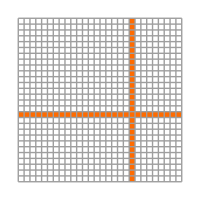

```mathematica
SparseArray[{{row,_}->1.,{_,col}->1.},{28,28}]
MatrixPlot[%,ImageSize->200,Mesh->All,Frame->False]
```

SparseArray[…]

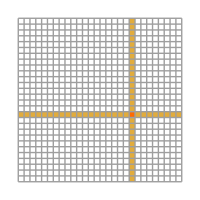

SparseArray[…]

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,2,1.,1.,1.,1.,1.,1.,1.,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0}

```mathematica
SparseArray[{{row,col}->2,{row,_}->1.,{_,col}->1.},{28,28}]
MatrixPlot[%,ImageSize->200,Mesh->All,Frame->False]
Flatten@%%
Normal@%
```

```mathematica
ClearAll[Feature]
Feature@{row_,}:=Flatten@SparseArray[{row,_}->1.,{28,28}]
Feature@{,col_}:=Flatten@SparseArray[{_,col}->1.,{28,28}]
Feature@{row_,col_}:=Flatten@SparseArray[{{row,col}->2,{row,_}->1.,{_,col}->1.},{28,28}]
```

```mathematica
Normal@Feature@{,col};
```

```mathematica
Feature@{row,col}.Train[[2,12]]
```

1229.

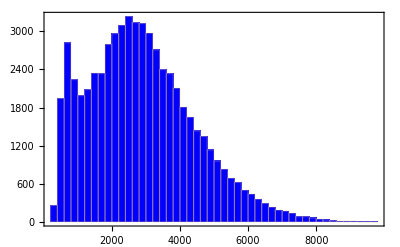

```mathematica
Histogram[Dot[Train[[2]],Feature@{row,col}],50,ChartStyle->{Blue},Frame->True,PlotRange->All]
```

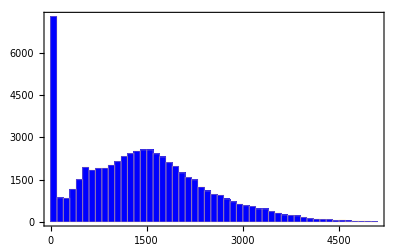

```mathematica
Histogram[Dot[Train[[2]],Feature@{,col}],50,ChartStyle->{Blue},Frame->True,PlotRange->All]
```

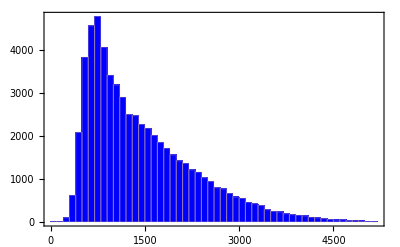

```mathematica
Histogram[Dot[Train[[2]],Feature@{row,}],50,ChartStyle->{Blue},Frame->True,PlotRange->All]
```

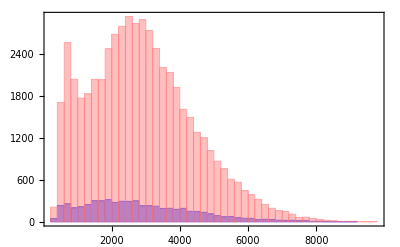

```mathematica
Histogram[{#[[indFriend]],#[[indFoe]]},40,ChartStyle->{Blue,Pink},Frame->True,PlotRange->All]&@Dot[Train[[2]],Feature@{row,col}]
```

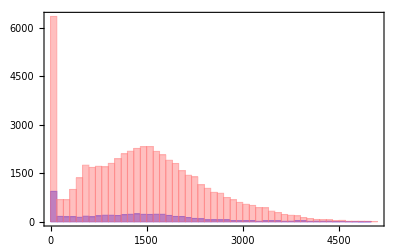

```mathematica
Histogram[{#[[indFriend]],#[[indFoe]]},40,ChartStyle->{Blue,Pink},Frame->True,PlotRange->All]&@Dot[Train[[2]],Feature@{,col}]
```

```mathematica
Partition[Train[[2,12]],28]//MatrixPlot;
```

## Задание 3

```mathematica
Through@{Mean,StandardDeviation}@N@Train[[2,indFriend,ind]]
```

{46.4291,85.2224}

```mathematica
Through@{Mean,StandardDeviation}@N@Train[[2,indFoe,ind]]
```

{80.7585,105.344}

```mathematica
Dot[Train[[2,indFriend]],Feature@{row,col}];
Through@{Mean,StandardDeviation}@N@%
```

{2857.79,1658.88}

```mathematica
Dot[Train[[2,indFoe]],Feature@{row,col}];
Through@{Mean,StandardDeviation}@N@%
```

{2871.13,1525.91}

```mathematica
Dot[Train[[2,indFriend]],Feature@{row,}];
Through@{Mean,StandardDeviation}@N@%
```

{1565.81,848.17}

```mathematica
Dot[Train[[2,indFoe]],Feature@{row,}];
Through@{Mean,StandardDeviation}@N@%
```

{1434.12,848.815}

```mathematica
Dot[Train[[2,indFriend]],Feature@{,col}];
Through@{Mean,StandardDeviation}@N@%
```

{1291.98,1037.03}

```mathematica
Dot[Train[[2,indFoe]],Feature@{,col}];
Through@{Mean,StandardDeviation}@N@%
```

{1437.01,973.214}

```mathematica
Through@{Mean,StandardDeviation}@N@Train[[2,#,ind]]&/@{indFriend,indFoe}
```

{{46.4291,85.2224},{80.7585,105.344}}

```mathematica
Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{row,col}]&/@{indFriend,indFoe}
```

{{2857.79,1658.88},{2871.13,1525.91}}

```mathematica
Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{,col}]&/@{indFriend,indFoe}
```

{{1291.98,1037.03},{1437.01,973.214}}

```mathematica
Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{row,}]&/@{indFriend,indFoe}
```

{{1565.81,848.17},{1434.12,848.815}}

```mathematica
friends=Through@{Through@{Mean,StandardDeviation}@N@Train[[2,#,ind]]&,Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{row,}]&,Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{,col}]&,Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{row,col}]&}@indFriend
```

{{46.4291,85.2224},{1565.81,848.17},{1291.98,1037.03},{2857.79,1658.88}}

```mathematica
strangers=Through@{Through@{Mean,StandardDeviation}@N@Train[[2,#,ind]]&,Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{row,}]&,Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{,col}]&,Through@{Mean,StandardDeviation}@N@Dot[Train[[2,#]],Feature@{row,col}]&}@indFoe
```

{{80.7585,105.344},{1434.12,848.815},{1437.01,973.214},{2871.13,1525.91}}

```mathematica
Length@friends
```

4

```mathematica
friends[[1,1]]
```

46.4291

```mathematica
muFr=friends[[#,1]]&/@Range[Length@friends]//N(*мю для объектов свой: пиксель, строка, столбец, крест*)
```

{46.4291,1565.81,1291.98,2857.79}

```mathematica
muFoe=strangers[[#,1]]&/@Range[Length@strangers]//N(*мю для объектов чужой: пиксель, строка, столбец, крест*)
```

{80.7585,1434.12,1437.01,2871.13}

```mathematica
stdFr=friends[[#,2]]&/@Range[Length@friends]//N
stdFoe=strangers[[#,2]]&/@Range[Length@strangers]//N
(*стандартное отклонение для объектов чужой, свой соответственно: пиксель, строка, столбец, крест*)
```

{85.2224,848.17,1037.03,1658.88}

{105.344,848.815,973.214,1525.91}

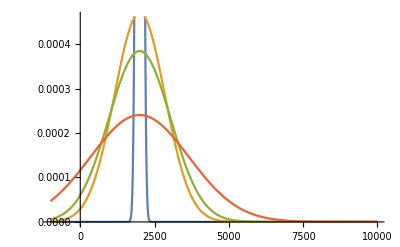

```mathematica
figSFr=Plot[Table[PDF[NormalDistribution[2000,σ],x],{σ,stdFr}]//Evaluate,{x,-1000,10000}]
```

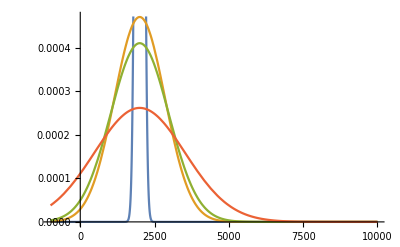

```mathematica
figSFoe=Plot[Table[PDF[NormalDistribution[2000,σ],x],{σ,stdFoe}]//Evaluate,{x,-1000,10000}]
```

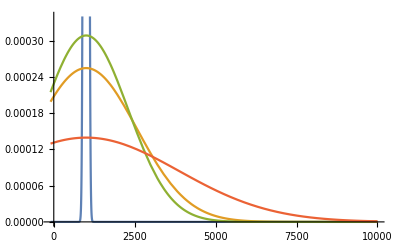

```mathematica
figMFr=Plot[Table[PDF[NormalDistribution[1000,μ],x],{μ,muFr}]//Evaluate,{x,-100,10000}]
```

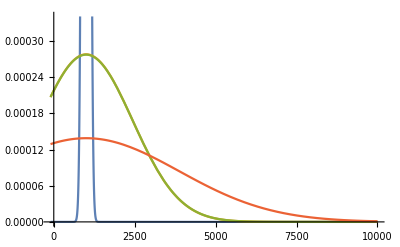

```mathematica
figMFoe=Plot[Table[PDF[NormalDistribution[1000,μ],x],{μ,muFoe}]//Evaluate,{x,-100,10000}]
```

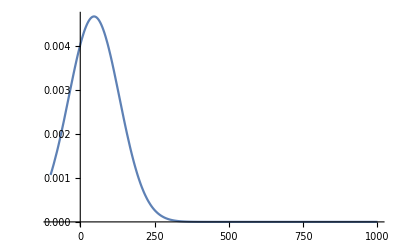

```mathematica
Plot[{PDF[NormalDistribution[muFr[[1]],stdFr[[1]]],x]},{x,-100,1000}]
```

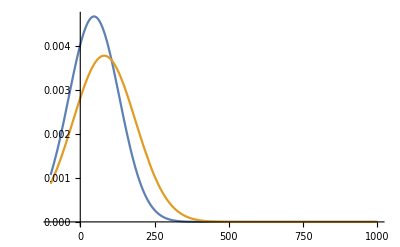

```mathematica
Plot[{PDF[NormalDistribution[muFr[[1]],stdFr[[1]]],x],PDF[NormalDistribution[muFoe[[1]],stdFoe[[1]]],x]},{x,-100,1000}]
```

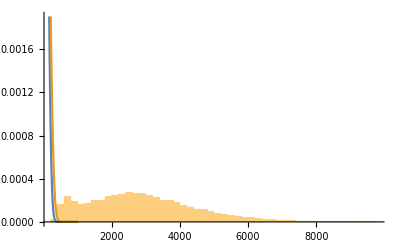

```mathematica
Show[
Histogram[Dot[Train[[2]],Feature@{row,col}],50,"PDF"],
Plot[{PDF[NormalDistribution[muFr[[1]],stdFr[[1]]],x],PDF[NormalDistribution[muFoe[[1]],stdFoe[[1]]],x]},{x,-1000,1000}]]
```

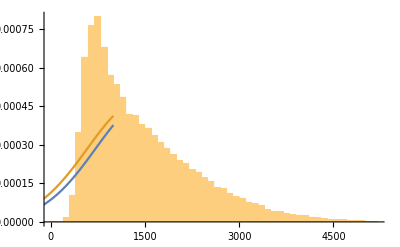

```mathematica
Show[
Histogram[Dot[Train[[2]],Feature@{row,}],50,"PDF"],
Plot[{PDF[NormalDistribution[muFr[[2]],stdFr[[2]]],x],PDF[NormalDistribution[muFoe[[2]],stdFoe[[2]]],x]},{x,-1000,1000}]]
```

## Задание 4

```mathematica
muRow=Table[Mean[Dot[Train[[2]],Feature@{i,}]],{i,1,28}](*средние значения скан-строк*)
```

{0.0136833,1.73925,28.5863,105.001,368.286,794.814,1184.37,1444.08,1512.79,1437.12,1328.43,1286.92,1339.23,1441.18,1524.1,1528.,1447.18,1343.23,1303.5,1340.18,1392.37,1362.21,1171.69,831.721,402.743,146.311,51.0282,4.83423}

```mathematica
sigmRow=Table[StandardDeviation[Dot[Train[[2]],Feature@{i,}]],{i,1,28}](*стандартные отклонения скан-строк*)
```

{2.38151,27.2968,123.222,276.786,524.736,742.28,849.201,830.954,865.469,863.388,769.439,677.404,674.059,733.01,803.535,852.66,849.656,818.239,832.94,878.263,891.315,866.658,827.349,690.047,493.591,288.123,161.229,47.0334}

```mathematica
muCol=Table[Mean[Dot[Train[[2]],Feature@{,i}]],{i,1,28}](*средние значения скан-столбцов*);
sigmCol = Table[StandardDeviation[Dot[Train[[2]],Feature@{,i}]],{i,1,28}](*стандартные отклонения скан-столбцов*);
```

```mathematica
Table[w1=(Feature@{i,}-muRow[[i]])/sigmRow[[i]],{i,1,28}];
```

```mathematica
Table[w2=(Feature@{,i}-muCol[[i]])/sigmCol[[i]],{i,1,28}];
```

```mathematica
W=Thread[List[w1,w2]](*веса всех потанциальных нейронов первого слоя*);
```

```mathematica
Dimensions[W]
```

{784,2}

## Задание 5

```mathematica
muRowFr=Table[Mean[Dot[Train[[2,indFriend]],Feature@{i,}]],{i,1,28}];
muRowFoe=Table[Mean[Dot[Train[[2,indFoe]],Feature@{i,}]],{i,1,28}];
sigmRowFr=Table[StandardDeviation[Dot[Train[[2,indFriend]],Feature@{i,}]],{i,1,28}];
sigmRowFoe=Table[StandardDeviation[Dot[Train[[2,indFoe]],Feature@{i,}]],{i,1,28}];
```

```mathematica
qRow=Abs[muRowFr-muRowFoe]/(sigmRowFr+sigmRow);
```

```mathematica
muColFr=Table[Mean[Dot[Train[[2,indFriend]],Feature@{,i}]],{i,1,28}];
muColFoe=Table[Mean[Dot[Train[[2,indFoe]],Feature@{,i}]],{i,1,28}];
sigmColFr=Table[StandardDeviation[Dot[Train[[2,indFriend]],Feature@{,i}]],{i,1,28}];
sigmColFoe=Table[StandardDeviation[Dot[Train[[2,indFoe]],Feature@{,i}]],{i,1,28}];
```

```mathematica
qCol=Abs[muColFr-muColFoe]/(sigmColFr+sigmColFoe);
```

```mathematica
qRow[[1;;5]]
```

{0.00637804,0.0707291,0.257523,0.416829,0.693261}

```mathematica
qCol[[1;;5]]
```

{0.00733136,0.0352375,0.0720944,0.0815568,0.111161}

```mathematica
W1=TakeLargest[Flatten@{qRow,qCol},50]
```

{0.798218,0.758155,0.693261,0.654181,0.638328,0.527058,0.444466,0.416933,0.416829,0.36249,0.332023,0.317269,0.310094,0.307349,0.289119,0.287882,0.264681,0.260884,0.260338,0.259353,0.257523,0.240962,0.233829,0.205854,0.205242,0.198964,0.161942,0.15877,0.158516,0.155175,0.153758,0.152951,0.147132,0.129593,0.124978,0.122763,0.120664,0.111161,0.109994,0.0950161,0.0926699,0.0815568,0.0775645,0.0721446,0.0720944,0.0709686,0.0707291,0.0701192,0.0647967,0.0555178}

## Задание 6

## Советы и подсказки

### Subsection. Загрузка базы растров MNIST

В каталоге  MNIST (см.[1]) приведены растры 28×28 рукописных цифр “0”–“9”.  База данных каталога находится в файлах: “train-images.idx3-ubyte”, “train-labels.idx1-ubyte” — 60 000 образцов тренировочного набора (Train) и “t10k-images.idx3-ubyte”, “t10k-labels.idx1-ubyte” — 10 000 образцов тестового набора (Test). Сами файлы и описание их структуры можно найти на сайте http://yann.lecun.com/exdb/mnist/index.html.

```mathematica
SetDirectory@NotebookDirectory[];
```

#### Subsection.Subsubsection. Загрузка набора растров ИмяНабора↦{Цифры,Растры}

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Partition[BinaryReadList[F,"Byte",ByteOrdering->+1],Rows Cols];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

#### Subsection.Subsubsection. Загрузка тренировочных шаблонов TrainLabel→TrainImage

```mathematica
Map[Dimensions,Train=LoadMNIST["MNIST\\train"]]
```

{{60000},{60000,784}}

#### Subsection.Subsubsection. Загрузка проверочных шаблонов TestLabel→TestImage

```mathematica
Map[Dimensions,Test=LoadMNIST["MNIST\\t10k"]]
```

{{10000},{10000,784}}

#### Subsection.Subsubsection. Загруженные наборы шаблонов

```mathematica
DynamicModule[{m=4},Grid[{
{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{
Manipulate[Style[Train⟦1,n⟧,Bold,24+2m]->Image[Partition[256-Train⟦2,n⟧,28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,37267,"Train"},1,Length@Train⟦1⟧,1,Appearance->"Labeled"},Paneled->False],
Manipulate[Style[Test⟦1,n⟧,Bold,24+2m]->Image[Partition[256-Test⟦2,n⟧,28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,4655,"Test"},1,Length@Test⟦1⟧,1,Appearance->"Labeled"},Paneled->False]}},Frame->All,FrameStyle->Gray]]
```